```mathematica
(* some functions memoize their values, so if you want fresh start, clear them all *)
ClearAll["ONinAdS`CFT`*"]
ClearAll["ONinAdS`ONsinglet`"]
ClearAll["ONinAdS`ONrank2`*"]
(* this loads the package with all function definitions *)
<< ONinAdS`
```

ONinAdS` package loaded.

## General Showcase

### Show all provided functions

```mathematica
??ONinAdS`CFT`*
```

```mathematica
??ONinAdS`ONsinglet`*
```

```mathematica
??ONinAdS`ONrank2`*
```

### Demonstrate some of them

```mathematica
?B2d
(* note that internal variables are encapsulated in the package context *)
```

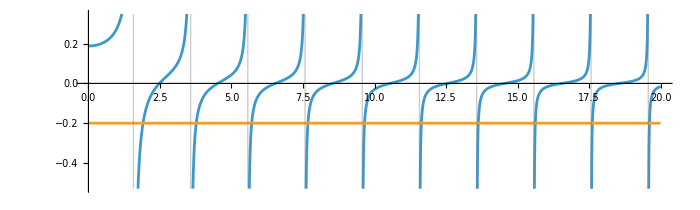

```mathematica
Plot[{Evaluate@FullSimplify[2B2d[9/7,2/2+z]],-1/λ /. λ->5},{z,0,20},
ImageSize->700,AspectRatio->0.3,MaxRecursion->8,ExclusionsStyle->Directive[Gray,Opacity[0.4]]]
```

```mathematica
?eq2d
eq2d[5/2,10]
```

1/10+(PolyGamma[0,5/2-(ONinAdS`ONsinglet`Private`Δ)/2]-PolyGamma[0,3/2+(ONinAdS`ONsinglet`Private`Δ)/2])/(4 π-4 π ONinAdS`ONsinglet`Private`Δ)

```mathematica
?polesList2d
polesList2d[5/2,10][[;;100]] // N // EchoTiming
```

8.10768

{5.26746,7.21711,9.1765,11.147,13.1254,15.109,17.0963,19.0862,21.0779,23.0711,25.0654,27.0605,29.0562,31.0526,33.0493,35.0465,37.0439,39.0416,41.0396,43.0377,45.036,47.0345,49.033,51.0317,53.0305,55.0294,57.0283,59.0274,61.0265,63.0256,65.0248,67.0241,69.0234,71.0227,73.0221,75.0215,77.0209,79.0204,81.0199,83.0194,85.0189,87.0185,89.0181,91.0177,93.0173,95.0169,97.0166,99.0162,101.016,103.016,105.015,107.015,109.015,111.014,113.014,115.014,117.014,119.013,121.013,123.013,125.013,127.013,129.012,131.012,133.012,135.012,137.012,139.012,141.011,143.011,145.011,147.011,149.011,151.011,153.01,155.01,157.01,159.01,161.01,163.01,165.01,167.01,169.009,171.009,173.009,175.009,177.009,179.009,181.009,183.009,185.009,187.009,189.008,191.008,193.008,195.008,197.008,199.008,201.008,203.008}

```mathematica
?opeSqList2d
opeSqList2d[100,5/2,10]// N // EchoTiming
```

0.218732

{2.31375,2.95478,1.49998,0.470413,0.109199,0.0206227,0.00335092,0.000485597,0.0000643124,7.92077×10^-6,9.18861×10^-7,1.0138×10^-7,1.07185×10^-8,1.09241×10^-9,1.07839×10^-10,1.03516×10^-11,9.69347×10^-13,8.87908×10^-14,7.97378×10^-15,7.03418×10^-16,6.10579×10^-17,5.2225×10^-18,4.40729×10^-19,3.67368×10^-20,3.02755×10^-21,2.46898×10^-22,1.99395×10^-23,1.5958×10^-24,1.26642×10^-25,9.97147×10^-27,7.79356×10^-28,6.04933×10^-29,4.66503×10^-30,3.57554×10^-31,2.72471×10^-32,2.06504×10^-33,1.55701×10^-34,1.16823×10^-35,8.72459×10^-37,6.487×10^-38,4.80306×10^-39,3.54203×10^-40,2.60212×10^-41,1.90466×10^-42,1.3893×10^-43,1.01×10^-44,7.3192×10^-46,5.28779×10^-47,3.80897×10^-48,2.736×10^-49,1.95996×10^-50,1.40038×10^-51,9.98053×10^-53,7.09597×10^-54,5.03335×10^-55,3.56227×10^-56,2.51568×10^-57,1.77285×10^-58,1.24684×10^-59,8.75187×10^-61,6.13151×10^-62,4.28784×10^-63,2.99322×10^-64,2.08589×10^-65,1.45118×10^-66,1.00797×10^-67,6.9903×10^-69,4.8404×10^-70,3.34676×10^-71,2.3107×10^-72,1.59315×10^-73,1.09693×10^-74,7.54276×10^-76,5.17991×10^-77,3.5528×10^-78,2.43383×10^-79,1.66531×10^-80,1.13814×10^-81,7.76978×10^-83,5.29839×10^-84,3.60922×10^-85,2.456×10^-86,1.66956×10^-87,1.13381×10^-88,7.69231×10^-90,5.21387×10^-91,3.5307×10^-92,2.38873×10^-93,1.61468×10^-94,1.09051×10^-95,7.35876×10^-97,4.96157×10^-98,3.34257×10^-99,2.25007×10^-100,1.51347×10^-101,1.01723×10^-102,6.8319×10^-104,4.58506×10^-105,3.07495×10^-106,2.06075×10^-107}

```mathematica
?γ2d
γ2d[50,7/4,10,{0,1}]//N
```

-0.0301224

## Example — a Twist–Spin Plot in d=2

```mathematica
(* calculate anomalous dimensions for some chosen values of Δext and λ *)
Δext=E; λ=E^7;
nmax=4; Jmax=6;tmax=50;
γTable = Table[{n,J,N@γ2d[tmax,Δext,λ,{n,J}]},{n,0,nmax},{J,1,Jmax}] // EchoTiming
```

0.000161

{{{0,1,-0.109146},{0,2,-0.00952301},{0,3,-0.00196844},{0,4,-0.0005895},{0,5,-0.000219413},{0,6,-0.0000945616}},{{1,1,-0.15514},{1,2,-0.017962},{1,3,-0.00442531},{1,4,-0.0015017},{1,5,-0.000614158},{1,6,-0.000284969}},{{2,1,-0.178261},{2,2,-0.024439},{2,3,-0.00674398},{2,4,-0.00249513},{2,5,-0.00109263},{2,6,-0.000535912}},{{3,1,-0.190797},{3,2,-0.0293259},{3,3,-0.0087578},{3,4,-0.00345141},{3,5,-0.00159166},{3,6,-0.00081514}},{{4,1,-0.197704},{4,2,-0.0330487},{4,3,-0.0104595},{4,4,-0.00432482},{4,5,-0.00207682},{4,6,-0.00110098}}}

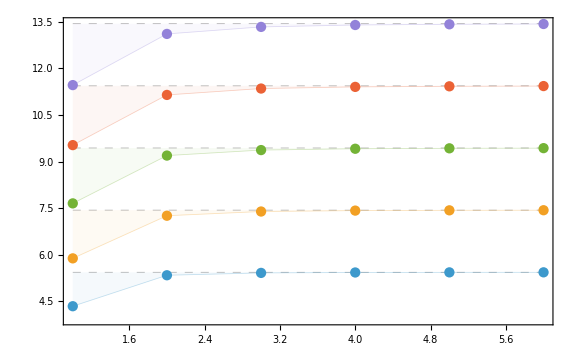

```mathematica
largeN=1/10; (* small N, such that anomalous dimension for J>=1 are visible *)
twistTable = Apply[{#2,2Δext+2#1+(1/largeN)#3}&,γTable,{2}]; (* calculate twists *)
MFTtwistTable = Apply[{#2,2Δext+2#1}&,γTable,{2}]; (* MFT twists (without anomalous dimensions) *)
(* generate twist-spin plot *)
twistPlot=ListPlot[twistTable]; 
twistLinePlot=ListLinePlot[twistTable,
PlotStyle->Directive[Opacity[0.3],Thickness[0.001]],Filling->Table[n->2Δext+2n-2,{n,1,nmax+1}],FillingStyle->Opacity[0.05]];
MFTtwistPlot=ListLinePlot[MFTtwistTable,
PlotStyle->Directive[Dashing[0.01],GrayLevel[0.7],Thickness[0.001]]];
Show[MFTtwistPlot,twistLinePlot,twistPlot,ImageSize->Large,PlotRange->{{1,Jmax},{2Δext-1.5,2Δext+2nmax}},Frame->True]
```